```mathematica
data=Import["mondayI.tsv"]
```

{{byCount,0,-7.452,41.5542,75.1,25.674},{byCount,30,-7.4523,41.5542,75.6,25.674},{byCount,60,-7.4527,41.5554,75.4,25.674},{byCount,90,-7.452,41.5554,75.4,25.841},2469,{byCount,48870,-7.4555,41.5638,95.3,7.49561},{byCount,48900,-7.4582,41.5646,95.4,8.24547},{byCount,48930,-7.4523,41.5654,95.7,8.57876}}
 |  |  |  |

```mathematica
foo=data[[All,3;; 5]]
```

{{-7.452,41.5542,75.1},{-7.4523,41.5542,75.6},{-7.4527,41.5554,75.4},{-7.452,41.5554,75.4},{-7.4531,41.5556,75.3},{-7.4528,41.5558,75.5},{-7.4507,41.5514,73.2},{-7.453,41.5517,72.3},{-7.4514,41.555,72.9},2459,{-7.4541,41.5596,94.5},{-7.4497,41.5592,95.7},{-7.4481,41.5629,96.7},{-7.4471,41.563,100.},{-7.4506,41.5639,98.8},{-7.4555,41.5638,95.3},{-7.4582,41.5646,95.4},{-7.4523,41.5654,95.7}}
 |  |  |  |

```mathematica
ListPointPlot3D[foo,Filling->Bottom]
```

-Graphics3D-

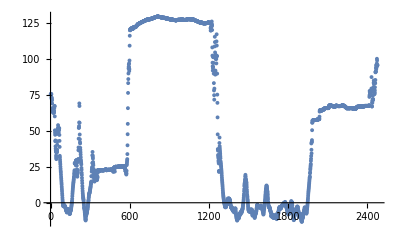

```mathematica
ListPlot[data[[All,5]] ]
```

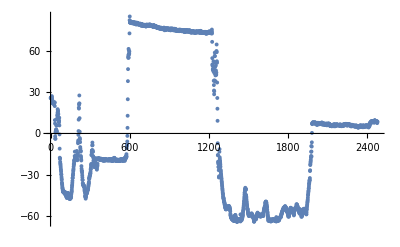

```mathematica
ListPlot[data[[All,6]] ]
```

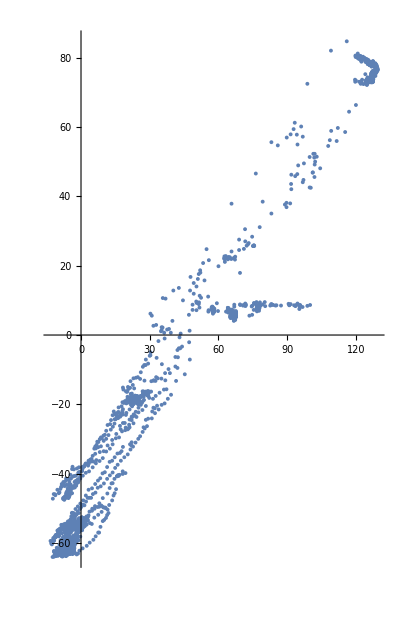

```mathematica
ListPlot[data[[All,5 ;; 6]],AspectRatio-> 1.55]
```

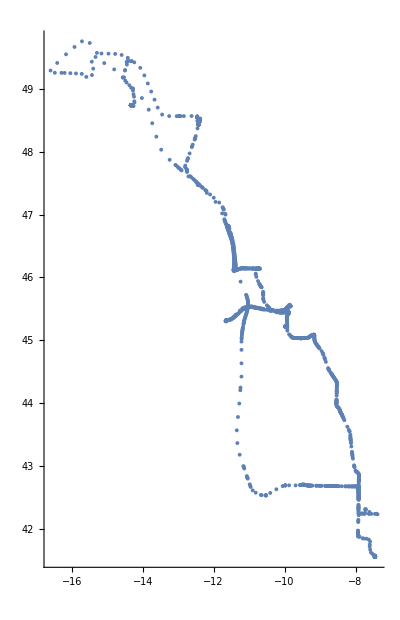

```mathematica
ListPlot[data[[All,3;;4]],AspectRatio-> 1.55]
```

```mathematica
data[[8]]
```

{byCount,210,-7.453,41.5517,72.3,25.7575}

```mathematica
q=Reverse[data[[10;;15]],2]
```

{{27.0095,71.7,41.5556,-7.4487,270,byCount},{24.8395,71.1,41.5582,-7.4525,300,byCount},{24.5057,69.,41.559,-7.4575,330,byCount},{24.0884,65.7,41.5607,-7.4575,360,byCount},{22.2527,64.5,41.5643,-7.4603,390,byCount},{22.503,64.4,41.5642,-7.4596,420,byCount}}

```mathematica
Options[ListPointPlot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,Epilog→{},FaceGrids→None,FaceGridsStyle→{},Filling→None,FillingStyle→Automatic,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,Method→Automatic,Method→Automatic,PlotLabel→None,PlotLegends→None,PlotRange→{Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→Fit,SphericalRegion→False,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},DisplayFunction:>$DisplayFunction,FormatType:>TraditionalForm,PlotTheme:>$PlotTheme}